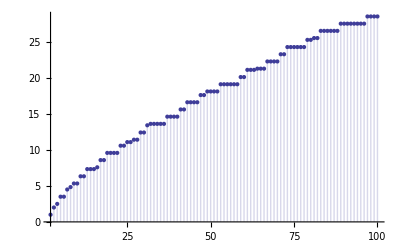

```mathematica
P[n_,k_,j_]:=1/k-P[n/j,k+1,Floor[n/j]]+P[n,k,j-1]
P[n_,k_,1]:=0
DiscretePlot[P[n,1,n],{n,2,100}]
```

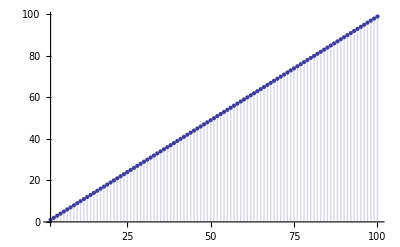

```mathematica
Q[n_,k_,j_]:=(MangoldtLambda[j]/Log[j])(1/(k!)+Q[n/j,k+1,Floor[n/j]])+Q[n,k,j-1]
Q[n_,k_,1]:=0
DiscretePlot[Q[n,1,n],{n,2,100}]
```

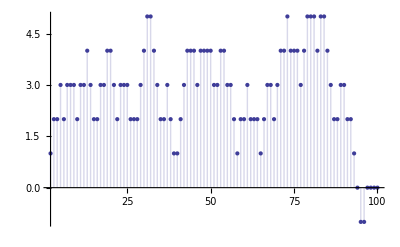

```mathematica
f2[n_,k_,j_]:=(MangoldtLambda[j]/Log[j])(1/(k!)-f2[n/j,k+1,Floor[n/j]])+f2[n,k,j-1]
f2[n_,k_,1]:=0
DiscretePlot[f2[n,1,n],{n,2,100}]
```

```mathematica
f3[n_,k_,j_]:=MoebiusMu[j](-1/k-f3[n/j,k+1,Floor[n/j]])+f3[n,k,j-1]
f3[n_,k_,1]:=0
DiscretePlot[f3[n,1,n],{n,2,100}]
```

-Graphics-

```mathematica
f4[n_,j_]:=MoebiusMu[j](-1-f4[n/j,Floor[n/j]])+f4[n,j-1]
f4[n_,1]:=0
DiscretePlot[f4[n,n],{n,2,100}]
```

-Graphics-

```mathematica
f5[n_,j_]:=1-f5[n/j,Floor[n/j]]+f5[n,j-1]
f5[n_,1]:=0
DiscretePlot[f5[n,n],{n,2,100}]
```

-Graphics-

```mathematica
MM[n_] := Sum[ MoebiusMu[j],{j,1,n}]
```

```mathematica
DiscretePlot[ 1-MM[n],{n,2,100}]
```

-Graphics-

```mathematica
f6[n_,k_,j_]:=BernoulliB[k]/(k!)+(MangoldtLambda[j]/Log[j])f6[n/j,k+1,Floor[n/j]]+f6[n,k,j-1]
f6[n_,k_,1]:=0
DiscretePlot[f6[n,0,n],{n,2,100}]
```

-Graphics-

```mathematica
V :={ -1,0.5,0.08333333333333331,0.041666666666666685,0.0263888888888889,0.01874999999999998,0.014269179894179898,0.01136739417989419,0.009356536596119918,0.007892554012345693,0.006785849984634702,0.00592405641233766,0.00523669325795029,0.004677498407042256,0.004214952239005476,0.0038268995532118833,0.0034973498453499227,0.003214496431323566,0.0029694477154582075,0.0027553902994367197,0.0025670225450072316,0.0024001623785907264,0.0022514701977588646,0.0021182495272954417,0.0019983012550434556,0.0018898154636787002,0.0017912900780718889,0.0017014689263700762,0.0016192940490963666,0.0015438685969283445 }
```

```mathematica
Part[V,1]
```

-1

```mathematica
f7[n_,k_,j_]:=-Part[V,k] Simplify[MangoldtLambda[j]/Log[j]]-f7[n/j,k+1,Floor[n/j]]+f7[n,k,j-1]
f7[n_,k_,1]:=0
DiscretePlot[f7[n,1,n],{n,2,100}]
```

-Graphics-

```mathematica
f7[n,1,n]-f7[n-1,1,n-1]
```

$Aborted